```mathematica
a={{{3,171827/500000},{17,3899/15625},{23,23551/100000},{29,56633/250000}},{{3,176959/500000},{19,33473/125000},{23,4078/15625},{29,32089/125000}},{{5,161707/500000},{11,4441/15625},{17,66591/250000},{29,24769/100000}},{{5,157463/500000},{11,136547/500000},{19,123151/500000},{23,12023/50000}},{{5,16927/50000},{11,153581/500000},{19,72323/250000},{29,140171/500000}},{{5,179421/500000},{11,8439/25000},{23,19909/62500},{29,32339/100000}},{{5,81829/250000},{13,35249/125000},{17,67911/250000},{23,131227/500000}},{{5,5307/15625},{13,75127/250000},{19,36053/125000},{23,71423/250000}},{{5,18587/50000},{17,167909/500000},{19,85269/250000},{23,171233/500000}},{{7,142611/500000},{11,129427/500000},{13,125089/500000},{19,57687/250000}},{{7,19543/62500},{11,145393/500000},{13,143699/500000},{23,133481/500000}},{{7,163161/500000},{11,19401/62500},{17,18351/62500},{19,148101/500000}},{{7,43653/125000},{11,42011/125000},{17,81919/250000},{23,32627/100000}},{{7,180047/500000},{11,87791/250000},{19,85151/250000},{23,43187/125000}},{{7,87367/250000},{13,165711/500000},{17,80873/250000},{19,165179/500000}},{{7,46619/125000},{13,36207/100000},{17,89961/250000},{23,181121/500000}},{{7,192139/500000},{13,2359/6250},{19,187079/500000},{23,763/2000}},{{7,52209/125000},{17,206009/500000},{19,211191/500000},{23,54211/125000}},{{11,5177/12500},{13,207833/500000},{17,208937/500000},{19,107909/250000}},{{11,54359/125000},{13,219517/500000},{17,8899/20000},{23,229173/500000}},{{11,223219/500000},{13,113441/250000},{19,229713/500000},{23,2963/6250}},{{11,119649/250000},{17,239651/500000},{19,24609/50000},{23,63663/125000}},{{13,124169/250000},{17,125179/250000},{19,257279/500000},{23,266901/500000}}}
```

{{{3,171827/500000},{17,3899/15625},{23,23551/100000},{29,56633/250000}},{{3,176959/500000},{19,33473/125000},{23,4078/15625},{29,32089/125000}},{{5,161707/500000},{11,4441/15625},{17,66591/250000},{29,24769/100000}},{{5,157463/500000},{11,136547/500000},{19,123151/500000},{23,12023/50000}},{{5,16927/50000},{11,153581/500000},{19,72323/250000},{29,140171/500000}},{{5,179421/500000},{11,8439/25000},{23,19909/62500},{29,32339/100000}},{{5,81829/250000},{13,35249/125000},{17,67911/250000},{23,131227/500000}},{{5,5307/15625},{13,75127/250000},{19,36053/125000},{23,71423/250000}},{{5,18587/50000},{17,167909/500000},{19,85269/250000},{23,171233/500000}},{{7,142611/500000},{11,129427/500000},{13,125089/500000},{19,57687/250000}},{{7,19543/62500},{11,145393/500000},{13,143699/500000},{23,133481/500000}},{{7,163161/500000},{11,19401/62500},{17,18351/62500},{19,148101/500000}},{{7,43653/125000},{11,42011/125000},{17,81919/250000},{23,32627/100000}},{{7,180047/500000},{11,87791/250000},{19,85151/250000},{23,43187/125000}},{{7,87367/250000},{13,165711/500000},{17,80873/250000},{19,165179/500000}},{{7,46619/125000},{13,36207/100000},{17,89961/250000},{23,181121/500000}},{{7,192139/500000},{13,2359/6250},{19,187079/500000},{23,763/2000}},{{7,52209/125000},{17,206009/500000},{19,211191/500000},{23,54211/125000}},{{11,5177/12500},{13,207833/500000},{17,208937/500000},{19,107909/250000}},{{11,54359/125000},{13,219517/500000},{17,8899/20000},{23,229173/500000}},{{11,223219/500000},{13,113441/250000},{19,229713/500000},{23,2963/6250}},{{11,119649/250000},{17,239651/500000},{19,24609/50000},{23,63663/125000}},{{13,124169/250000},{17,125179/250000},{19,257279/500000},{23,266901/500000}}}

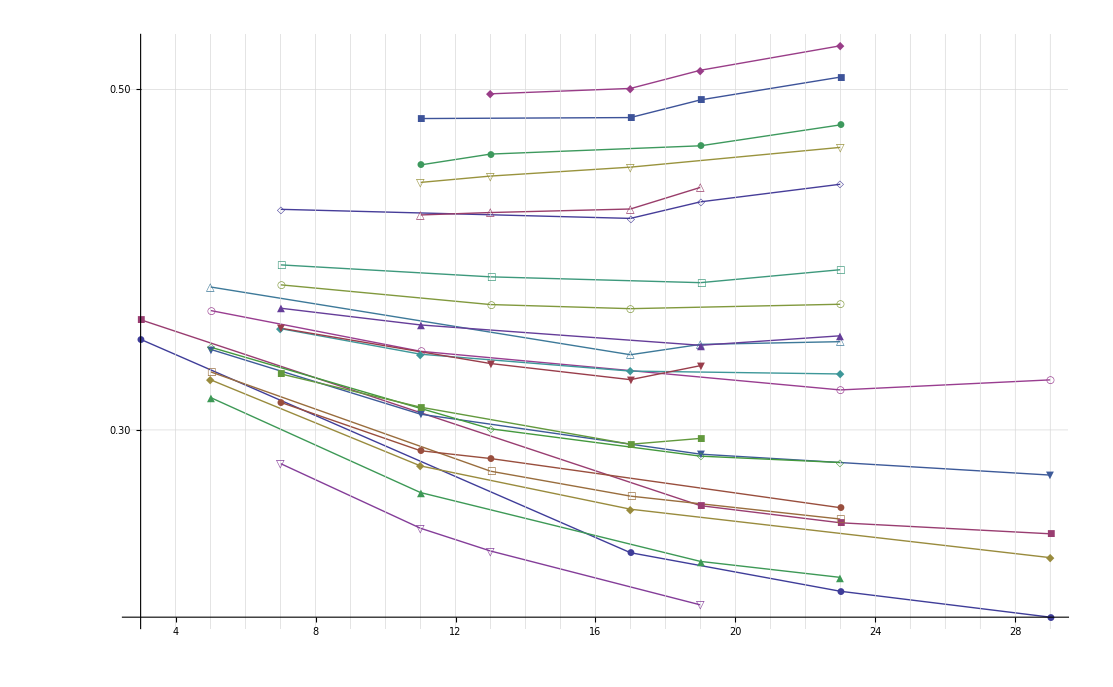

```mathematica
ListLogPlot[Select[a,Length[#]==4&], Joined->True,PlotMarkers->Automatic, GridLines->{Range[30],Range[0,1,0.01]}, PlotRange->{All,{0,1}}, PlotStyle->Thick]
```

```mathematica
Length[ReadList[ FileNameForVotedValues[{13,17,19,23}]]]
```

500001

```mathematica
Length[v]
```

1000

```mathematica
With[
{baseTuple = {13,17,19,23},
range=500000},
With[
{all =Monitor[ ReadList[ FileNameForVotedValues[baseTuple],Expression,range], "Reading"]},
TableForm[
Sort[
Table[
{tuple, Monitor[Last[Accumulate[Map[If[IsGoodForTuple[#,tuple] ,1,0]&, all]]], "Mapping " <> ToString[tuple]]}
, {tuple, Subsets[baseTuple, {1,4}]}
],
#1[[2]]>#2[[2]]&
],
TableDepth->2
]
]
]
```

{23} | 266901
{19} | 257279
{17} | 250358
{13} | 248338
{19,23} | 148878
{17,23} | 146563
{13,23} | 141419
{17,19} | 139771
{13,19} | 135497
{13,17} | 131436
{17,19,23} | 104194
{13,19,23} | 100160
{13,17,23} | 98386
{13,17,19} | 95225
{13,17,19,23} | 77288

```mathematica
N[magicGraham[{13,17,19,23}]]
```

0.108699

```mathematica
With[
{baseTuple = {7,11,13,19},
range=5000000},
With[
{all =Monitor[ ReadList[ FileNameForVotedValues[baseTuple],Expression,range], "Reading"]},
TableForm[
Sort[
Table[
{tuple, Monitor[Sum[value,{value,Map[If[IsGoodForTuple[#,tuple] ,1,0]&, all]}], "Mapping " <> ToString[tuple]]}
, {tuple, Subsets[baseTuple, {1,4}]}
],
#1[[2]]>#2[[2]]&
],
TableDepth->2
]
]
]
```

{{{3,171951/500000},{13,65781/250000},{29,14023/62500},{31,56359/250000}},{{3,171827/500000},{17,3899/15625},{23,23551/100000},{29,56633/250000}},{{3,34983/100000},{17,131167/500000},{23,24929/100000},{31,11971/50000}},{{3,18357/50000},{17,151457/500000},{29,70663/250000},{31,148309/500000}},{{3,176959/500000},{19,33473/125000},{23,4078/15625},{29,32089/125000}},{{3,179807/500000},{19,70181/250000},{23,137779/500000},{31,134531/500000}},{{3,187901/500000},{19,160147/500000},{29,76593/250000},{31,16091/50000}},{{3,38913/100000},{23,87237/250000},{29,86829/250000},{31,91187/250000}},{{5,2003/6250},{7,9477/31250},{29,59051/250000},{31,12031/50000}},{{5,161707/500000},{11,4441/15625},{17,66591/250000},{29,24769/100000}},{{5,33063/100000},{11,14763/50000},{17,34771/125000},{31,16359/62500}},{{5,157463/500000},{11,136547/500000},{19,123151/500000},{23,12023/50000}},{{5,16927/50000},{11,153581/500000},{19,72323/250000},{29,140171/500000}},{{5,6853/20000},{11,39193/125000},{19,37159/125000},{31,35819/125000}},{{5,179421/500000},{11,8439/25000},{23,19909/62500},{29,32339/100000}},{{5,4561/12500},{11,8621/25000},{23,164611/500000},{31,8279/25000}},{{5,2381/6250},{11,92789/250000},{29,89273/250000},{31,187089/500000}},{{5,81829/250000},{13,35249/125000},{17,67911/250000},{23,131227/500000}},{{5,6943/20000},{13,39307/125000},{17,154529/500000},{29,9337/31250}},{{5,176329/500000},{13,80419/250000},{17,79347/250000},{31,154509/500000}},{{5,5307/15625},{13,75127/250000},{19,36053/125000},{23,71423/250000}},{{5,45031/125000},{13,166679/500000},{19,20371/62500},{29,161397/500000}},{{5,47023/125000},{13,179863/500000},{23,173979/500000},{29,35663/100000}},{{5,18587/50000},{17,167909/500000},{19,85269/250000},{23,171233/500000}},{{5,24211/62500},{17,183631/500000},{19,23599/62500},{29,189769/500000}},{{5,2033/5000},{17,200717/500000},{23,200577/500000},{29,8333/20000}},{{5,208771/500000},{19,207083/500000},{23,209649/500000},{29,218367/500000}},{{7,142611/500000},{11,129427/500000},{13,125089/500000},{19,57687/250000}},{{7,19543/62500},{11,145393/500000},{13,143699/500000},{23,133481/500000}},{{7,33797/100000},{11,160933/500000},{13,32019/100000},{29,152279/500000}},{{7,163161/500000},{11,19401/62500},{17,18351/62500},{19,148101/500000}},{{7,43653/125000},{11,42011/125000},{17,81919/250000},{23,32627/100000}},{{7,9327/25000},{11,457/1250},{17,22583/62500},{29,181689/500000}},{{7,180047/500000},{11,87791/250000},{19,85151/250000},{23,43187/125000}},{{7,192419/500000},{11,9543/25000},{19,94607/250000},{29,191871/500000}},{{7,101219/250000},{11,202203/500000},{23,201827/500000},{29,333/800}},{{7,87367/250000},{13,165711/500000},{17,80873/250000},{19,165179/500000}},{{7,46619/125000},{13,36207/100000},{17,89961/250000},{23,181121/500000}},{{7,197923/500000},{13,7809/20000},{17,1961/5000},{29,199233/500000}},{{7,192139/500000},{13,2359/6250},{19,187079/500000},{23,763/2000}},{{7,204271/500000},{13,1633/4000},{19,25627/62500},{29,104977/250000}},{{7,212147/500000},{13,42947/100000},{23,215089/500000},{29,5559/12500}},{{7,52209/125000},{17,206009/500000},{19,211191/500000},{23,54211/125000}},{{7,272/625},{17,217671/500000},{19,225383/500000},{29,230201/500000}},{{7,56783/125000},{17,232499/500000},{23,236779/500000},{29,245241/500000}},{{7,57977/125000},{19,29777/62500},{23,121541/250000},{29,126269/250000}},{{11,5177/12500},{13,207833/500000},{17,208937/500000},{19,107909/250000}},{{11,54359/125000},{13,219517/500000},{17,8899/20000},{23,229173/500000}},{{11,113829/250000},{13,231443/500000},{17,47213/100000},{29,246297/500000}},{{11,223219/500000},{13,113441/250000},{19,229713/500000},{23,2963/6250}},{{11,233371/500000},{13,4777/10000},{19,1947/4000},{29,253277/500000}},{{11,241819/500000},{13,247153/500000},{23,126763/250000},{29,131821/250000}},{{11,119649/250000},{17,239651/500000},{19,24609/50000},{23,63663/125000}},{{11,124871/250000},{17,15789/31250},{19,8139/15625},{29,270773/500000}},{{11,259147/500000},{17,6581/12500},{23,135077/250000},{29,281299/500000}},{{11,262939/500000},{19,267829/500000},{23,1101/2000},{29,287023/500000}},{{13,124169/250000},{17,125179/250000},{19,257279/500000},{23,266901/500000}},{{13,129557/250000},{17,262441/500000},{19,54103/100000},{29,283301/500000}},{{13,268343/500000},{17,272473/500000},{23,280793/500000},{29,146299/250000}},{{13,136501/250000},{19,55441/100000},{23,285593/500000},{29,18593/31250}},{{17,70861/125000},{19,288737/500000},{23,148843/250000},{29,310799/500000}}}

$Aborted